# Two-Dimensional Kolmogorov flow

## With large-scale drag

### Basic equations

The Kolmogorov flow can be described by the following equation for the stream function

∂_t ∇^2 ψ= -sin(y)∂_x (ψ+∇^2 ψ)+1/R∇^4 ψ-(∂_y ψ∂_x -∂_x ψ∂_y)∇^2 ψ-μ ∇^2 ψ
∂_t ∇^2 ψ= -ℒ ψ + N(ψ)

We propose the following Ansatz to solve this equation

ψ=∑_(n=-∞)^∞ c_n e^(iαx+iny)

If we consider only the linear equation we derive a set infinite ordinary differential equations

∂_t ∇^2 ψ= -ℒ ψ 
(α^2+n^2)d/dt c_n=-((α^2+n^2)^2)/R c_n+a/2(c_(n+1)(α^2+(n-1)^2-1)-c_(n-1)(α^2+(n+1)^2-1))

We consider only the first vertical modes, namely we cut the series in n=1. The operator ℒ takes the following matrix form

ℒ=((-(α^2+1)^2)/R | α/2(α^2-1)  | 0
-α^3/2 | -α^4/R | α^3/2
0 | -α/2(α^2-1) | (-(α^2+1)^2)/R)

### Computation of the eigenvalues and eigenvectors

#### Highest eigenvalue

To study  the stability of the laminar solution, we look for the highest eigenvalue of the operator ℒ

```mathematica
ℒ[R_, μ_]:={{-(1+ α^2)^2/R, α/2(α^2-1), 0},{-α^3/2, -α^4/R-μ α^2 , α^3/2},{0, -α/2(α^2-1), -(1+α^2)^2/R}}
```

```mathematica
Eigenvalues[ℒ[R,μ]]
```

{-((1+α^2)^2)/R,(-R-2 R α^2-2 R α^4-R^2 α^2 μ-√(R^2+4 R^2 α^2+4 R^2 α^4+2 R^4 α^4-2 R^4 α^6-2 R^3 α^2 μ-4 R^3 α^4 μ+R^4 α^4 μ^2))/(2 R^2),(-R-2 R α^2-2 R α^4-R^2 α^2 μ+√(R^2+4 R^2 α^2+4 R^2 α^4+2 R^4 α^4-2 R^4 α^6-2 R^3 α^2 μ-4 R^3 α^4 μ+R^4 α^4 μ^2))/(2 R^2)}

The highest eigenvalue is given by

```mathematica
Subscript[λ, max]=(-R-2 R α^2-2 R α^4-R^2 α^2 μ+√(R^2+4 R^2 α^2+4 R^2 α^4+2 R^4 α^4-2 R^4 α^6-2 R^3 α^2 μ-4 R^3 α^4 μ+R^4 α^4 μ^2))/(2 R^2)
```

(-R-2 R α^2-2 R α^4-R^2 α^2 μ+√(R^2+4 R^2 α^2+4 R^2 α^4+2 R^4 α^4-2 R^4 α^6-2 R^3 α^2 μ-4 R^3 α^4 μ+R^4 α^4 μ^2))/(2 R^2)

We compute the critical stability curve R_c(α)  by setting the above equation equal to zero

```mathematica
Solve[Subscript[λ, max]==0,R]
```

{{R→(-2 μ-4 α^2 μ-2 α^4 μ-√(-4 (-α^2+α^4) (2 α^2+4 α^4+2 α^6)+(2 μ+4 α^2 μ+2 α^4 μ)^2))/(2 (-α^2+α^4))},{R→(-2 μ-4 α^2 μ-2 α^4 μ+√(-4 (-α^2+α^4) (2 α^2+4 α^4+2 α^6)+(2 μ+4 α^2 μ+2 α^4 μ)^2))/(2 (-α^2+α^4))}}

The only physical solution is given by

```mathematica
Subscript[R, c][α_, μ_]:=(μ(1+α^2)^2+√(2 α^4(1-α^2)(1+α^2)^2 +μ^2(1+α^2)^4))/((1-α^2)α^2)
PlotRc0 = Plot[Subscript[R, c][α,0],{α, 0, .99}, PlotStyle->Red];
Manipulate[Show[{Plot[Subscript[R, c][α,μ],{α, 0, .99}, PlotRange->{{0,.99},{0,10}}], PlotRc0}], {μ, 0,.1}]
```

#### Most unstable eigenfunction

We can define the most unstable eigenfunction, which we will label ψ_α

```mathematica
Eigensystem[ℒ[Subscript[R, c][α,μ],μ ]]
```

{{0,(α (-α-α^3+α^5+α^7))/(μ+2 α^2 μ+α^4 μ+√(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))),(α (-2 α-2 α^3+4 α^7-2 α μ^2-4 α^3 μ^2-2 α^5 μ^2-2 α μ √(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))))/(2 (μ+2 α^2 μ+α^4 μ+√(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))))},{{-1,(2 (α+2 α^3+α^5))/(μ+2 α^2 μ+α^4 μ+√(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))),1},{1,0,1},{-(2 (α^4+α^6-α^8-α^10+μ^2+4 α^2 μ^2+6 α^4 μ^2+4 α^6 μ^2+α^8 μ^2+μ √(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))+2 α^2 μ √(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))+α^4 μ √(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))))/((μ+2 α^2 μ+α^4 μ+√(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2)))^2),-(2 α^5-2 α^7+2 α μ^2+4 α^3 μ^2+2 α^5 μ^2+2 α μ √(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2)))/(μ+α^2 μ-α^4 μ-α^6 μ+√(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))-α^2 √(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))),1}}}

```mathematica
ψα[α_,μ_,x_,y_]=(Exp[I α x + I y] - Exp[I α x - I y])  +(2 (α+2 α^3+α^5))/(μ+2 α^2 μ+α^4 μ+√(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2)))Exp[I α  x]
```

-ⅇ^(-ⅈ y+ⅈ x α)+ⅇ^(ⅈ y+ⅈ x α)+(2 ⅇ^(ⅈ x α) (α+2 α^3+α^5))/(μ+2 α^2 μ+α^4 μ+√(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2)))

A physical stream function will be given by the real part of ψ_α. We now plot this eigenfunction, and its combination with the laminar solution

```mathematica
Manipulate[ContourPlot[Re[ψα[1/3,μ,x,y]],{x,0,6 π},{y,0, 2 π}, AspectRatio->1/3]  ,{μ,0,.1}]
```

```mathematica
Manipulate[ContourPlot[-Cos[y]+A Re[ψα[1/3,μ,x,y]],{x,0,6 π},{y,0, 2 π}, AspectRatio->1/3] ,{A,0,2},{μ,0,.1}]
```

We note that we can express the unstable eigenvector in the following way as well

ψ_α=e^(iαx+iy)-e^(iαx-iy)+R_c0^2/(α R_c)e^iαx

Therefore for computation purposes we define

```mathematica
ψαc=((Exp[ I y] - Exp[- I y])  + Rc0^2/(α Rc)) Exp[I α x]
```

ⅇ^(ⅈ x α) (-ⅇ^(-ⅈ y)+ⅇ^(ⅈ y)+Rc0^2/(Rc α))

```mathematica
Manipulate[Show[{Plot[(Subscript[R, c][α,0])^2/Subscript[R, c][α,μ]/α,{α, 0, .99}, PlotRange->{{0,.99},{0,10}}]}], {μ, 0,.1}]
```

Where the sub index c stands for “computation”.

#### Weakly non-linear analysis

#### Ansatz

We now derive a formal equation for the amplitude A of the most unstable eigenfunction close to the onset of instability. We propose the following Ansatz

ψ=A ψ_α+A^*ψ_α^*+W(A,A^*)
∂_t A=f^[2]+f^[3]+...
W = W^[2]+W^[3]+...

We put the Ansatz in Mathematica format for making the upcoming computations

```mathematica
ψ = Refine[A ψαc+ Conjugate[A ψαc],Assumptions->{α ∈Reals, x ∈Reals, y ∈Reals, Rc ∈Reals, Rc0 ∈Reals}]
```

A ⅇ^(ⅈ x α) (-ⅇ^(-ⅈ y)+ⅇ^(ⅈ y)+Rc0^2/(Rc α))+ⅇ^(-ⅈ x α) (ⅇ^(-ⅈ y)-ⅇ^(ⅈ y)+Rc0^2/(Rc α)) Conjugate[A]

Where the super index [n] denotes the order of the term in powers of, we will get these terms order by order. For these computation we will need the following functions

```mathematica
Lap[exp_]:=D[exp, {x,2}] + D[exp, {y,2}] 
Bilap[exp_]:=Lap[Lap[exp]]
NL[exp_]:= -(D[exp, {y,1}]D[Lap[exp], {x,1}]-D[exp, {x,1}]D[Lap[exp], {y,1}])
```

These functions correspond to the Laplacian, Bilaplacian and the non-linear term of the full stream function equation.

#### Order 2

We start by computing the left hand side of the equation, we need to take the Laplacian of ψ_α

```mathematica
Collect[Lap[ψαc],{Exp[I y]}, Simplify]
```

-(ⅇ^(ⅈ x α) Rc0^2 α)/Rc+ⅇ^(-ⅈ y+ⅈ x α) (1+α^2)-ⅇ^(ⅈ y+ⅈ x α) (1+α^2)

We also need to compute the non-linear term up to second order in A

```mathematica
NL2 = Collect[NL[ψ],{Exp[I α x],Exp[-I  α x],Exp[ 2I α x], Exp[- 2I α x]}, Simplify]
```

(A^2 ⅇ^(-ⅈ y+2 ⅈ x α) (1+ⅇ^(2 ⅈ y)) Rc0^2)/Rc-(2 A ⅇ^(-ⅈ y) (1+ⅇ^(2 ⅈ y)) Rc0^2 Conjugate[A])/Rc+(ⅇ^(-ⅈ y-2 ⅈ x α) (1+ⅇ^(2 ⅈ y)) Rc0^2 Conjugate[A]^2)/Rc

Summing up we have

-f^[2]((Rc0^2 α)/Rc+(1+α^2)(e^iy-e^-iy))e^iαx -(f^*)^[2]((Rc0^2 α)/Rc-(1+α^2)(e^iy-e^-iy))e^-iαx= -2|A|^2 Rc0^2/Rc(e^iy+e^-iy)+A^2 Rc0^2/Rc e^(2iαx)(e^iy+e^-iy)+(A^*)^2 Rc0^2/Rc e^(-2iαx)(e^iy+e^-iy)- ℒ W^[2]

Re -arranging

ℒ W^[2]=b^[2]

Where

b^[2]=f^[2]((Rc0^2 α)/Rc+(1+α^2)(e^iy-e^-iy))e^iαx +(f^*)^[2]((Rc0^2 α)/Rc-(1+α^2)(e^iy-e^-iy))e^-iαx-2|A|^2 Rc0^2/Rc(e^iy+e^-iy)+A^2 Rc0^2/Rc e^(2iαx)(e^iy+e^-iy)+(A^*)^2 Rc0^2/Rc e^(-2iαx)(e^iy+e^-iy)

```mathematica
b2 = f2((Rc0^2 α)/Rc+(1+α^2)(Exp[I y]-Exp[-I y]))Exp[I α x] +Conjugate[f2]((Rc0^2 α)/Rc-(1+α^2)(Exp[-I y]-Exp[I y]))Exp[-I α x]-2A Conjugate[A] Rc0^2/Rc(Exp[I y]+Exp[-I y])+A^2 Rc0^2/Rc Exp[2I α x](Exp[I y]+Exp[-I y])+Conjugate[A]^2 Rc0^2/Rc Exp[-2I α x](Exp[I y]+Exp[-I y])
```

(A^2 ⅇ^(2 ⅈ x α) (ⅇ^(-ⅈ y)+ⅇ^(ⅈ y)) Rc0^2)/Rc+ⅇ^(ⅈ x α) f2 ((Rc0^2 α)/Rc+(-ⅇ^(-ⅈ y)+ⅇ^(ⅈ y)) (1+α^2))-(2 A (ⅇ^(-ⅈ y)+ⅇ^(ⅈ y)) Rc0^2 Conjugate[A])/Rc+(ⅇ^(-2 ⅈ x α) (ⅇ^(-ⅈ y)+ⅇ^(ⅈ y)) Rc0^2 Conjugate[A]^2)/Rc+ⅇ^(-ⅈ x α) ((Rc0^2 α)/Rc-(ⅇ^(-ⅈ y)-ⅇ^(ⅈ y)) (1+α^2)) Conjugate[f2]

To find and expression for f^[2], we impose a solvability condition for the linear equation. This implies the following

⟨v|b^[2]⟩=0       ∀ v ∈ Ker{ℒ^†}

Where ⟨·|·⟩ is inner product we need to specify. The adjoint of the operator depends on this inner product. We define the following inner product

⟨g|f⟩ = α/(4 π^2)(∫_0)^((2π)/α)(∫_0)^(2π)g^*(x,y)f(x,y)ⅆxⅆy

```mathematica
InnerProduct[exp1_,exp2_]:=Refine[α/(4 π^2)Integrate[Integrate[exp2 Conjugate[exp1],{x,0, (2π)/α}],{y,0,2π }], Assumptions->{α∈Reals, Rc ∈Reals, x ∈Reals, y ∈Reals}]
```

With this inner product the adjoint of the operator ℒ is just the transposed matrix

ℒ^†=((-(α^2+1)^2)/R | -α^3/2 | 0
α/2(α^2-1)  | -α^4/R-μ α^2 | -α/2(α^2-1)
0 | α^3/2 | (-(α^2+1)^2)/R)

We need to determine the Kernel of this operator

```mathematica
ℒdagger[R_]:=Transpose[ℒ[R,μ]]
Eigensystem[ℒdagger[Subscript[R, c][α,μ]]]
```

{{0,(α (-α-α^3+α^5+α^7))/(μ+2 α^2 μ+α^4 μ+√(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))),(α (-2 α-2 α^3+4 α^7-2 α μ^2-4 α^3 μ^2-2 α^5 μ^2-2 α μ √(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))))/(2 (μ+2 α^2 μ+α^4 μ+√(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))))},{{-1,-(2 (-1-α^2+α^4+α^6))/(α (μ+2 α^2 μ+α^4 μ+√(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2)))),1},{1,0,1},{-((2 (α^4+α^6-α^8-α^10+μ^2+4 α^2 μ^2+6 α^4 μ^2+4 α^6 μ^2+α^8 μ^2+μ √((1+α^2)^2 (2 α^4-2 α^6+μ^2+2 α^2 μ^2+α^4 μ^2))+2 α^2 μ √((1+α^2)^2 (2 α^4-2 α^6+μ^2+2 α^2 μ^2+α^4 μ^2))+α^4 μ √((1+α^2)^2 (2 α^4-2 α^6+μ^2+2 α^2 μ^2+α^4 μ^2))))/(μ+2 α^2 μ+α^4 μ+√((1+α^2)^2 (2 α^4-2 α^6+μ^2+2 α^2 μ^2+α^4 μ^2)))^2),-(2 α^4-2 α^6+2 μ^2+4 α^2 μ^2+2 α^4 μ^2+2 μ √(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2)))/(α μ+2 α^3 μ+α^5 μ+α √(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2))),1}}}

We have that Kernel of the adjoint operator is given by the following vector

ψ_α^†=(ⅇ^(ⅈ y)-ⅇ^(-ⅈ y)+(2 (1+α^2-α^4-α^6))/(α (μ+2 α^2 μ+α^4 μ+√(-(1+α^2)^2 (-2 α^4+2 α^6-μ^2-2 α^2 μ^2-α^4 μ^2)))))ⅇ^(ⅈ x α) 
ψ_α^†=(ⅇ^(ⅈ y)-ⅇ^(-ⅈ y)+(1-α^2)/α^3 R_c)ⅇ^(ⅈ x α)

For computation purposes we define

```mathematica
ψαdaggerc=Refine[((Exp[ I y] - Exp[- I y])  + (1-α^2)1/α^3(Rc0)^2/Rc) Exp[I α x], Assumptions->Rc0 ∈Reals];
```

We impose the solvability condition

⟨ψ_α^†|b^[2]⟩=0

```mathematica
InnerProduct[ψαdaggerc,b2]
```

(f2 (2 (α^2+α^4)-(-1+α^2) Conjugate[Rc0]^2))/α^2

We conclude that  f^[2]=0. Now we can be sure that the linear system has a solution

ℒ W^[2]=b^[2]

The system can be easily be solved because b^[2]is made out of eigenvectors of ℒ

W^[2] = -R_c0^2/((1+4 α^2)^2)A^2 e^(2iαx)(e^iy+e^-iy)-R_c0^2/((1+4 α^2)^2)(A^*)^2 e^(-2iαx)(e^iy+e^-iy)+2 R_c0^2|A|^2(e^iy+e^-iy)

```mathematica
W2 = Refine[-Rc0^2/((1+4 α^2)^2)A^2 Exp[2I α x](Exp[I y]+Exp[-I y])-Rc0^2/((1+4 α^2)^2)Conjugate[A]^2 Exp[-2I α x](Exp[I y]+Exp[-I y])+2 Rc0^2 A Conjugate[A](Exp[I y]+Exp[-I y]), Assumptions->Rc0 ∈Reals];
```

#### Order 3

We incorporate the second order correction the Ansatz

```mathematica
ψ2 = Refine[A ψαc+ Conjugate[A ψαc]+W2,Assumptions->{α ∈Reals, x ∈Reals, y ∈Reals, Rc ∈Reals,Rc0 ∈Reals}];
```

We compute the non-linear terms up to order three, and we omit the lowest order terms since they get cancelled with the correction

```mathematica
NL3 =Collect[NL[ψ2]-NL[ψ],{Exp[I α x],Exp[-I  α x],Exp[ 2I α x], Exp[- 2I α x],,Exp[ 3I α x], Exp[- 3I α x],,Exp[ 4I α x], Exp[- 4I α x]}, Simplify];
```

We get the following system

ℒ W^[3]=b^[3]

```mathematica
b3 =  f3((Rc0^2 α)/Rc+(1+α^2)(Exp[I y]-Exp[-I y]))Exp[I α x]+ Conjugate[f3]((Rc0^2 α)/Rc-(1+α^2)(Exp[-I y]-Exp[I y]))Exp[-I α x] +NL3;
```

We impose the solvability condition

⟨ψ_α^†|b^[3]⟩=0

```mathematica
KernelProjection3 = InnerProduct[ψαdaggerc,b3]
```

1/(α^2 (Rc+4 Rc α^2)^2)(f3 (1+4 α^2)^2 (2 Rc^2 α^2 (1+α^2)-(-1+α^2) Abs[Rc0]^4)+2 A Rc α^2 Abs[A]^2 (Rc0^4 (3+17 α^2+16 α^4-32 α^6)+(-1+17 α^2+16 α^4-32 α^6) Abs[Rc0]^4))

```mathematica
Solve[KernelProjection3==0, f3]
```

{{f3→(2 A Rc α^2 Abs[A]^2 (-3 Rc0^4-17 Rc0^4 α^2-16 Rc0^4 α^4+32 Rc0^4 α^6+Abs[Rc0]^4-17 α^2 Abs[Rc0]^4-16 α^4 Abs[Rc0]^4+32 α^6 Abs[Rc0]^4))/((1+4 α^2)^2 (2 Rc^2 α^2+2 Rc^2 α^4+Abs[Rc0]^4-α^2 Abs[Rc0]^4))}}

```mathematica
Refine[(2 A Rc α^2 Abs[A]^2 (-3 Rc0^4-17 Rc0^4 α^2-16 Rc0^4 α^4+32 Rc0^4 α^6+Abs[Rc0]^4-17 α^2 Abs[Rc0]^4-16 α^4 Abs[Rc0]^4+32 α^6 Abs[Rc0]^4))/((1+4 α^2)^2 (2 Rc^2 α^2+2 Rc^2 α^4+Abs[Rc0]^4-α^2 Abs[Rc0]^4)), Assumptions->Rc0 ∈ Reals]
```

(2 A Rc α^2 Abs[A]^2 (-3 Rc0^4-17 Rc0^4 α^2-16 Rc0^4 α^4+32 Rc0^4 α^6+Abs[Rc0]^4-17 α^2 Abs[Rc0]^4-16 α^4 Abs[Rc0]^4+32 α^6 Abs[Rc0]^4))/((1+4 α^2)^2 (2 Rc^2 α^2+2 Rc^2 α^4+Abs[Rc0]^4-α^2 Abs[Rc0]^4))

#### Unfolding

We now perturb the critical Reynolds number R_c

R=R_c+∆R

This changes the Bilaplacian prefactor

1/R=1/(R+∆R)=1/R_c-(∆R)/(R_c+∆R)=1/R_c-ϵ

So the linear operator now reads

ℒ=ℒ_0-ϵ∇^4

Where ℒ_0 is the original linear operator. We change our Ansatz

ψ=A ψ_α+A^*ψ_α^*+W(A,A^*)
∂_t A=(ϵ f^[1,1]+ϵ^2 f^[1,2]+ϵ^3 f^[1,3]...)+(f^[3,0]+ϵ f^[3,1]+ϵ^2 f^[3,2]+...)+...
W = (ϵ W^[1,1]+ϵ^2 W^[1,2]+ϵ^3 W^[1,3]...)+ (W^[2,0]+ϵ W^[2,1]+ϵ^2 W^[2,2]+...)+...

We already calculated f^[3,0] and W^[2,0],  we just need to compute f^[1,0] and W^[1,0] to have all terms of the same order. We need to compute ∇^4  ψ_α to compute this terms.

```mathematica
Bilap[ψαc]
```

ⅇ^(ⅈ x α) (-ⅇ^(-ⅈ y)+ⅇ^(ⅈ y))-2 ⅇ^(ⅈ x α) (ⅇ^(-ⅈ y)-ⅇ^(ⅈ y)) α^2+ⅇ^(ⅈ x α) (-ⅇ^(-ⅈ y)+ⅇ^(ⅈ y)+Rc/α) α^4

We get the following linear system

ℒ W^[1,1]=b^[1,1]

```mathematica
b11 = Refine[-Bilap[ψ]+f11(Rc α+(1+α^2)(Exp[I y]-Exp[-I y]))Exp[I α x] +Conjugate[f11](Rc α-(1+α^2)(Exp[-I y]-Exp[I y]))Exp[-I α x] , Assumptions->{α ∈ Reals, Rc ∈ Reals}]
```

-A ⅇ^(ⅈ x α) (-ⅇ^(-ⅈ y)+ⅇ^(ⅈ y))+2 A ⅇ^(ⅈ x α) (ⅇ^(-ⅈ y)-ⅇ^(ⅈ y)) α^2-A ⅇ^(ⅈ x α) (-ⅇ^(-ⅈ y)+ⅇ^(ⅈ y)+Rc/α) α^4+ⅇ^(ⅈ x α) f11 (Rc α+(-ⅇ^(-ⅈ y)+ⅇ^(ⅈ y)) (1+α^2))-ⅇ^(-ⅈ x α) (ⅇ^(-ⅈ y)-ⅇ^(ⅈ y)) Conjugate[A]+2 ⅇ^(-ⅈ x α) (-ⅇ^(-ⅈ y)+ⅇ^(ⅈ y)) α^2 Conjugate[A]-ⅇ^(-ⅈ x α) (ⅇ^(-ⅈ y)-ⅇ^(ⅈ y)+Rc/α) α^4 Conjugate[A]+ⅇ^(-ⅈ x α) (Rc α-(ⅇ^(-ⅈ y)-ⅇ^(ⅈ y)) (1+α^2)) Conjugate[f11]

We impose the solvability condition

⟨ψ_α^†|b^[1,1]⟩=0

```mathematica
KernelProjection11 = InnerProduct[ψαdaggerc,b11]
```

-(A α^2 (-Rc^2 (-1+α^2)+2 (1+α^2)^2)+f11 (Rc^2 (-1+α^2)-2 (α^2+α^4)))/α^2

```mathematica
Solve[KernelProjection11==0, f11]
```

```mathematica
{{f11->(A α^2 (2+Rc^2+4 α^2-Rc^2 α^2+2 α^4))/(Rc^2+2 α^2-Rc^2 α^2+2 α^4)}}
```

{{f11→(A α^2 (2+Rc^2+4 α^2-Rc^2 α^2+2 α^4))/(Rc^2+2 α^2-Rc^2 α^2+2 α^4)}}

the final equation for the amplitude reads

τ ∂_t A= ϵ̄ A - γ|A|^2 A

τ = (Rc^2+2 α^2-Rc^2 α^2+2 α^4)/ α^2 
ϵ̄=ϵ (2+Rc^2+4 α^2-Rc^2 α^2+2 α^4) 
γ=(4 Rc^3  (1+17 α^2+16 α^4-32 α^6))/((1+4 α^2)^2)

Therefore, the stationary amplitude is given by

|A|= √((ϵ̄)/γ)=√ϵ  √((2+Rc^2+4 α^2-Rc^2 α^2+2 α^4)/(Rc^3  (1+17 α^2+16 α^4-32 α^6)(1+4 α^2)^2))

Let us compare this with the data from DNS

```mathematica
data = Import["/home/btph/bt307732/Projects/Kolmogorov flow/Two_Dimensional_Flow/merged_data.csv","Data"];
ReynoldsVsAmplitude=Drop[data, None,{2}];
```

```mathematica
dataplt =ListPlot[ReynoldsVsAmplitude, PlotMarkers->{{"*",20}}, PlotStyle->Red];
Re2D[Re_]:=Re^2/(2 π)^3
amplitudeCoeff = {√((2+Rc^2+4 α^2-Rc^2 α^2+2 α^4)/(Rc^3  (1+17 α^2+16 α^4-32 α^6)(1+4 α^2)^2))*Sqrt[InnerProduct[ψαc,ψαc]]}/.{α->1/3, Rc->Subscript[R, c][1/3]};
```

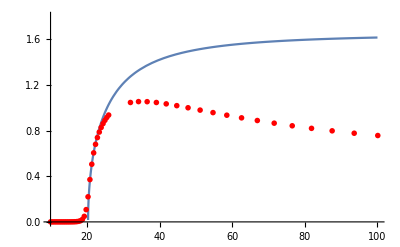

```mathematica
predictedPlt = Plot[Sqrt[(Re2D[x]-Subscript[R, c][1/3])/(Subscript[R, c][1/3]Re2D[x])]amplitudeCoeff,{x, 20, 100}, PlotRange->{{10,100},{0,1.8}}];
Show[predictedPlt, dataplt]
```

```mathematica
Manipulate[ContourPlot[-Cos[y]+ Sqrt[(Re2D[r]-Subscript[R, c][1/3])/(Subscript[R, c][1/3]Re2D[r])]amplitudeCoeff Re[ψα[1/3,x,y]],{x,0,6 π},{y,0, 2 π}, AspectRatio->1/3] ,{r,Sqrt[Subscript[R, c][1/3](2 π)^3] ,25}]
```

```mathematica
Rc0^2
```

Rc0^2